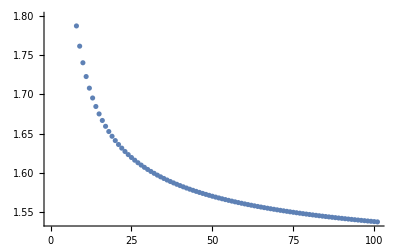

```mathematica
(* Michael Barile
MATH 68500
Fourier Coefficients *)

(* Crank Nicholson for lambda = .35, .40, .45, .50, .55, we see that it satisfies stability conditions *)

(* lambda = .35 *)

alpha=.35;
deltax=.1;
deltat=.01;
lambda=alpha*deltat/deltax^2;

(* vector of x values from -5 to 5 in steps of deltax = 0.1 *)
xvec={-5};
x0=-5;
While[Max[xvec]<5,
x=x0+deltax;
AppendTo[xvec,x];
x0=x;
];
For[i=1,i≤Length[xvec],++i,
If[Abs[xvec[[i]]]<10^-5,
xvec[[i]]=0
];
];

(* temperature values along rod at time t = 0 *)
uvec={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[uvec,20],
AppendTo[uvec,0]
];
];

(* Constructing matrix A *)

A={};
For[i=1,i≤Length[xvec],++i,
inew={};
For[j=1,j≤Length[xvec],++j,
If[j==i,
AppendTo[inew,2*(1-lambda)],
If[j==i-1||j==i+1,
AppendTo[inew,lambda],
AppendTo[inew,0]
];
];
];
AppendTo[A,inew]
];

(* Constructing and replacing top and bottom rows in matrix A to fix the first and last entry of uvec *)

toprow={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[toprow,1],
AppendTo[toprow,0]
];
];

bottomrow={};
For[i=1,i≤Length[xvec],++i,
If[i==Length[xvec],
AppendTo[bottomrow,1],
AppendTo[bottomrow,0]
];
];
A[[1]]=toprow;
A[[Length[xvec]]]=bottomrow; 
A=(1/2)*A;

(* Constructing A1, whose inverse B will take us from (n+1/2)th state to (n+1)th state. *)

A1={};
For[i=1,i≤Length[xvec],++i,
inew={};
For[j=1,j≤Length[xvec],++j,
If[j==i,
AppendTo[inew,2*(1+lambda)],
If[j==i-1||j==i+1,
AppendTo[inew,-lambda],
AppendTo[inew,0]
];
];
];
AppendTo[A1,inew]
];

(* Constructing and replacing top and bottom rows in matrix A1 to fix the first and last entry of uvec *)

toprow={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[toprow,1],
AppendTo[toprow,0]
];
];

bottomrow={};
For[i=1,i≤Length[xvec],++i,
If[i==Length[xvec],
AppendTo[bottomrow,1],
AppendTo[bottomrow,0]
];
];
A1[[1]]=toprow;
A1[[Length[xvec]]]=bottomrow; 
A1=(1/2)*A1;

B=Inverse[A1];


(* DFT *)

M = 101;
dftm = {};

For[k =0, k ≤ M -1, ++k, 
row = {};
For[i =0, i ≤ M-1, ++i,
xi = 2*Pi/M * i;
AppendTo[row, E^(-I*k*xi)] (* using negative sign here *)
];
AppendTo[dftm,row];
];

dftm=Simplify[dftm];
dftm=dftm/Sqrt[M];

(* uvectors including initial state and next 100 time steps *)

uvectors={uvec};
uvec0=uvec;
For[i=1,i≤100,++i,
uvec0=B.A.uvec0;
AppendTo[uvectors,uvec0]
];

(* determining Fourier Coefficients and storing vector of coefficients at each time step in a vector *)

fourcoef={};
For[i=1,i≤Length[uvectors],++i,
AppendTo[fourcoef,dftm.uvectors[[i]]]
];

(* extracting element twenty five from each coefficient vector in fourcoef *)

coef25={};
For[i=1,i≤Length[fourcoef],++i,
AppendTo[coef25,fourcoef[[i]][[25]]]
];

(* finding norm of above coefficient at each time step *)

normcoef25={};
For[i=1,i≤Length[coef25],++i,
AppendTo[normcoef25,Norm[coef25[[i]]]]
];


ListPlot[normcoef25]
```

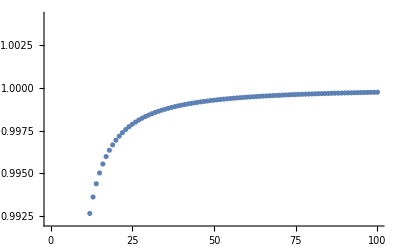

```mathematica
normratio25={};
For[i=1,i≤Length[normcoef25]-1,++i,
AppendTo[normratio25,normcoef25[[i+1]]/normcoef25[[i]]]
];



Show[ListPlot[normratio25]]
```

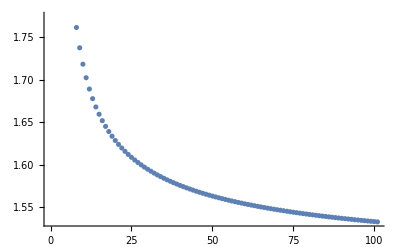

```mathematica
(***********************************************************************************)

(* lambda at .40 *)

alpha=.40;
deltax=.1;
deltat=.01;
lambda=alpha*deltat/deltax^2;

(* Constructing matrix A *)

A={};
For[i=1,i≤Length[xvec],++i,
inew={};
For[j=1,j≤Length[xvec],++j,
If[j==i,
AppendTo[inew,2*(1-lambda)],
If[j==i-1||j==i+1,
AppendTo[inew,lambda],
AppendTo[inew,0]
];
];
];
AppendTo[A,inew]
];

(* Constructing and replacing top and bottom rows in matrix A to fix the first and last entry of uvec *)

toprow={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[toprow,1],
AppendTo[toprow,0]
];
];

bottomrow={};
For[i=1,i≤Length[xvec],++i,
If[i==Length[xvec],
AppendTo[bottomrow,1],
AppendTo[bottomrow,0]
];
];
A[[1]]=toprow;
A[[Length[xvec]]]=bottomrow; 
A=(1/2)*A;

(* Constructing A1, whose inverse B will take us from (n+1/2)th state to (n+1)th state. *)

A1={};
For[i=1,i≤Length[xvec],++i,
inew={};
For[j=1,j≤Length[xvec],++j,
If[j==i,
AppendTo[inew,2*(1+lambda)],
If[j==i-1||j==i+1,
AppendTo[inew,-lambda],
AppendTo[inew,0]
];
];
];
AppendTo[A1,inew]
];

(* Constructing and replacing top and bottom rows in matrix A1 to fix the first and last entry of uvec *)

toprow={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[toprow,1],
AppendTo[toprow,0]
];
];

bottomrow={};
For[i=1,i≤Length[xvec],++i,
If[i==Length[xvec],
AppendTo[bottomrow,1],
AppendTo[bottomrow,0]
];
];
A1[[1]]=toprow;
A1[[Length[xvec]]]=bottomrow; 
A1=(1/2)*A1;

B=Inverse[A1];

(* DFT *)

M = 101;
dftm = {};

For[k =0, k ≤ M -1, ++k, 
row = {};
For[i =0, i ≤ M-1, ++i,
xi = 2*Pi/M * i;
AppendTo[row, E^(-I*k*xi)] (* using negative sign here *)
];
AppendTo[dftm,row];
];

dftm=Simplify[dftm];
dftm=dftm/Sqrt[M];

(* uvectors including initial state and next 100 time steps *)

uvectors={uvec};
uvec0=uvec;
For[i=1,i≤100,++i,
uvec0=B.A.uvec0;
AppendTo[uvectors,uvec0]
];

(* determining Fourier Coefficients and storing vector of coefficients at each time step in a vector *)

fourcoef={};
For[i=1,i≤Length[uvectors],++i,
AppendTo[fourcoef,dftm.uvectors[[i]]]
];

(* extracting element twenty five from each coefficient vector in fourcoef *)

coef25={};
For[i=1,i≤Length[fourcoef],++i,
AppendTo[coef25,fourcoef[[i]][[25]]]
];

(* finding norm of above coefficient at each time step *)

normcoef25={};
For[i=1,i≤Length[coef25],++i,
AppendTo[normcoef25,Norm[coef25[[i]]]]
];


ListPlot[normcoef25]
```

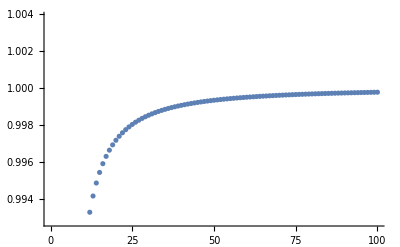

```mathematica
normratio25={};
For[i=1,i≤Length[normcoef25]-1,++i,
AppendTo[normratio25,normcoef25[[i+1]]/normcoef25[[i]]]
];


Show[ListPlot[normratio25]]
```

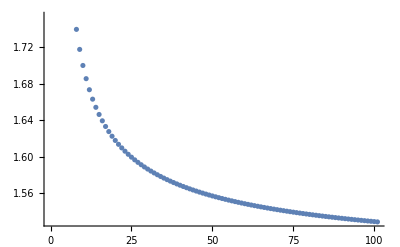

```mathematica
(************************************************************************************)
(* lambda at .45 *)

alpha=.45;
deltax=.1;
deltat=.01;
lambda=alpha*deltat/deltax^2;

(* Constructing matrix A *)

A={};
For[i=1,i≤Length[xvec],++i,
inew={};
For[j=1,j≤Length[xvec],++j,
If[j==i,
AppendTo[inew,2*(1-lambda)],
If[j==i-1||j==i+1,
AppendTo[inew,lambda],
AppendTo[inew,0]
];
];
];
AppendTo[A,inew]
];

(* Constructing and replacing top and bottom rows in matrix A to fix the first and last entry of uvec *)

toprow={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[toprow,1],
AppendTo[toprow,0]
];
];

bottomrow={};
For[i=1,i≤Length[xvec],++i,
If[i==Length[xvec],
AppendTo[bottomrow,1],
AppendTo[bottomrow,0]
];
];
A[[1]]=toprow;
A[[Length[xvec]]]=bottomrow; 
A=(1/2)*A;

(* Constructing A1, whose inverse B will take us from (n+1/2)th state to (n+1)th state. *)

A1={};
For[i=1,i≤Length[xvec],++i,
inew={};
For[j=1,j≤Length[xvec],++j,
If[j==i,
AppendTo[inew,2*(1+lambda)],
If[j==i-1||j==i+1,
AppendTo[inew,-lambda],
AppendTo[inew,0]
];
];
];
AppendTo[A1,inew]
];

(* Constructing and replacing top and bottom rows in matrix A1 to fix the first and last entry of uvec *)

toprow={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[toprow,1],
AppendTo[toprow,0]
];
];

bottomrow={};
For[i=1,i≤Length[xvec],++i,
If[i==Length[xvec],
AppendTo[bottomrow,1],
AppendTo[bottomrow,0]
];
];
A1[[1]]=toprow;
A1[[Length[xvec]]]=bottomrow; 
A1=(1/2)*A1;

B=Inverse[A1];

(* DFT *)

M = 101;
dftm = {};

For[k =0, k ≤ M -1, ++k, 
row = {};
For[i =0, i ≤ M-1, ++i,
xi = 2*Pi/M * i;
AppendTo[row, E^(-I*k*xi)] (* using negative sign here *)
];
AppendTo[dftm,row];
];

dftm=Simplify[dftm];
dftm=dftm/Sqrt[M];

(* uvectors including initial state and next 100 time steps *)

uvectors={uvec};
uvec0=uvec;
For[i=1,i≤100,++i,
uvec0=B.A.uvec0;
AppendTo[uvectors,uvec0]
];

(* determining Fourier Coefficients and storing vector of coefficients at each time step in a vector *)

fourcoef={};
For[i=1,i≤Length[uvectors],++i,
AppendTo[fourcoef,dftm.uvectors[[i]]]
];

(* extracting element twenty five from each coefficient vector in fourcoef *)

coef25={};
For[i=1,i≤Length[fourcoef],++i,
AppendTo[coef25,fourcoef[[i]][[25]]]
];

(* finding norm of above coefficient at each time step *)

normcoef25={};
For[i=1,i≤Length[coef25],++i,
AppendTo[normcoef25,Norm[coef25[[i]]]]
];


ListPlot[normcoef25]
```

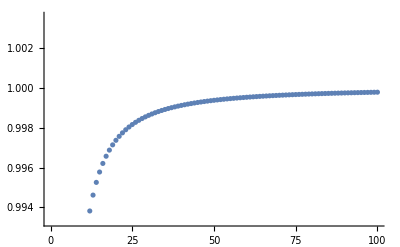

```mathematica
normratio25={};
For[i=1,i≤Length[normcoef25]-1,++i,
AppendTo[normratio25,normcoef25[[i+1]]/normcoef25[[i]]]
];

Show[ListPlot[normratio25]]

(* ratio of norms < 1*)
```

```mathematica
(************************************************************************************)
(* lambda = 0.5 *)
```

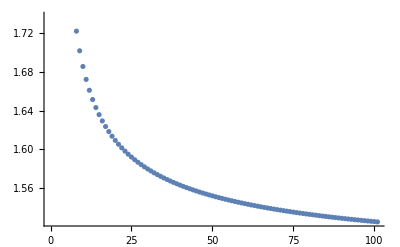

```mathematica
alpha=.50;
deltax=.1;
deltat=.01;
lambda=alpha*deltat/deltax^2;

(* Constructing matrix A *)

A={};
For[i=1,i≤Length[xvec],++i,
inew={};
For[j=1,j≤Length[xvec],++j,
If[j==i,
AppendTo[inew,2*(1-lambda)],
If[j==i-1||j==i+1,
AppendTo[inew,lambda],
AppendTo[inew,0]
];
];
];
AppendTo[A,inew]
];

(* Constructing and replacing top and bottom rows in matrix A to fix the first and last entry of uvec *)

toprow={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[toprow,1],
AppendTo[toprow,0]
];
];

bottomrow={};
For[i=1,i≤Length[xvec],++i,
If[i==Length[xvec],
AppendTo[bottomrow,1],
AppendTo[bottomrow,0]
];
];
A[[1]]=toprow;
A[[Length[xvec]]]=bottomrow; 
A=(1/2)*A;

(* Constructing A1, whose inverse B will take us from (n+1/2)th state to (n+1)th state. *)

A1={};
For[i=1,i≤Length[xvec],++i,
inew={};
For[j=1,j≤Length[xvec],++j,
If[j==i,
AppendTo[inew,2*(1+lambda)],
If[j==i-1||j==i+1,
AppendTo[inew,-lambda],
AppendTo[inew,0]
];
];
];
AppendTo[A1,inew]
];

(* Constructing and replacing top and bottom rows in matrix A1 to fix the first and last entry of uvec *)

toprow={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[toprow,1],
AppendTo[toprow,0]
];
];

bottomrow={};
For[i=1,i≤Length[xvec],++i,
If[i==Length[xvec],
AppendTo[bottomrow,1],
AppendTo[bottomrow,0]
];
];
A1[[1]]=toprow;
A1[[Length[xvec]]]=bottomrow; 
A1=(1/2)*A1;

B=Inverse[A1];

(* DFT *)

M = 101;
dftm = {};

For[k =0, k ≤ M -1, ++k, 
row = {};
For[i =0, i ≤ M-1, ++i,
xi = 2*Pi/M * i;
AppendTo[row, E^(-I*k*xi)] (* using negative sign here *)
];
AppendTo[dftm,row];
];

dftm=Simplify[dftm];
dftm=dftm/Sqrt[M];

(* uvectors including initial state and next 100 time steps *)

uvectors={uvec};
uvec0=uvec;
For[i=1,i≤100,++i,
uvec0=B.A.uvec0;
AppendTo[uvectors,uvec0]
];

(* determining Fourier Coefficients and storing vector of coefficients at each time step in a vector *)

fourcoef={};
For[i=1,i≤Length[uvectors],++i,
AppendTo[fourcoef,dftm.uvectors[[i]]]
];

(* extracting element twenty five from each coefficient vector in fourcoef *)

coef25={};
For[i=1,i≤Length[fourcoef],++i,
AppendTo[coef25,fourcoef[[i]][[25]]]
];

(* finding norm of above coefficient at each time step *)

normcoef25={};
For[i=1,i≤Length[coef25],++i,
AppendTo[normcoef25,Norm[coef25[[i]]]]
];


ListPlot[normcoef25]
```

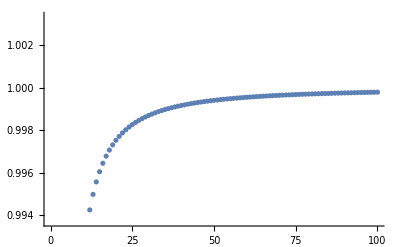

```mathematica
normratio25={};
For[i=1,i≤Length[normcoef25]-1,++i,
AppendTo[normratio25,normcoef25[[i+1]]/normcoef25[[i]]]
];

Show[ListPlot[normratio25]]
```

```mathematica
(**********************************************************************************)
(*lambda=.55*)
```

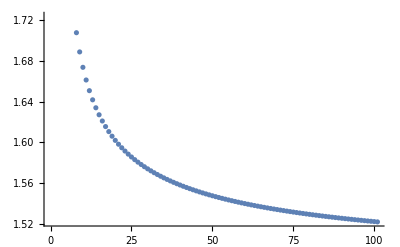

```mathematica
alpha=.55;
deltax=.1;
deltat=.01;
lambda=alpha*deltat/deltax^2;

(* Constructing matrix A *)

A={};
For[i=1,i≤Length[xvec],++i,
inew={};
For[j=1,j≤Length[xvec],++j,
If[j==i,
AppendTo[inew,2*(1-lambda)],
If[j==i-1||j==i+1,
AppendTo[inew,lambda],
AppendTo[inew,0]
];
];
];
AppendTo[A,inew]
];

(* Constructing and replacing top and bottom rows in matrix A to fix the first and last entry of uvec *)

toprow={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[toprow,1],
AppendTo[toprow,0]
];
];

bottomrow={};
For[i=1,i≤Length[xvec],++i,
If[i==Length[xvec],
AppendTo[bottomrow,1],
AppendTo[bottomrow,0]
];
];
A[[1]]=toprow;
A[[Length[xvec]]]=bottomrow; 
A=(1/2)*A;

(* Constructing A1, whose inverse B will take us from (n+1/2)th state to (n+1)th state. *)

A1={};
For[i=1,i≤Length[xvec],++i,
inew={};
For[j=1,j≤Length[xvec],++j,
If[j==i,
AppendTo[inew,2*(1+lambda)],
If[j==i-1||j==i+1,
AppendTo[inew,-lambda],
AppendTo[inew,0]
];
];
];
AppendTo[A1,inew]
];

(* Constructing and replacing top and bottom rows in matrix A1 to fix the first and last entry of uvec *)

toprow={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[toprow,1],
AppendTo[toprow,0]
];
];

bottomrow={};
For[i=1,i≤Length[xvec],++i,
If[i==Length[xvec],
AppendTo[bottomrow,1],
AppendTo[bottomrow,0]
];
];
A1[[1]]=toprow;
A1[[Length[xvec]]]=bottomrow; 
A1=(1/2)*A1;

B=Inverse[A1];

(* DFT *)

M = 101;
dftm = {};

For[k =0, k ≤ M -1, ++k, 
row = {};
For[i =0, i ≤ M-1, ++i,
xi = 2*Pi/M * i;
AppendTo[row, E^(-I*k*xi)] (* using negative sign here *)
];
AppendTo[dftm,row];
];

dftm=Simplify[dftm];
dftm=dftm/Sqrt[M];

(* uvectors including initial state and next 100 time steps *)

uvectors={uvec};
uvec0=uvec;
For[i=1,i≤100,++i,
uvec0=B.A.uvec0;
AppendTo[uvectors,uvec0]
];

(* determining Fourier Coefficients and storing vector of coefficients at each time step in a vector *)

fourcoef={};
For[i=1,i≤Length[uvectors],++i,
AppendTo[fourcoef,dftm.uvectors[[i]]]
];

(* extracting element twenty five from each coefficient vector in fourcoef *)

coef25={};
For[i=1,i≤Length[fourcoef],++i,
AppendTo[coef25,fourcoef[[i]][[25]]]
];

(* finding norm of above coefficient at each time step *)

normcoef25={};
For[i=1,i≤Length[coef25],++i,
AppendTo[normcoef25,Norm[coef25[[i]]]]
];


ListPlot[normcoef25]
```

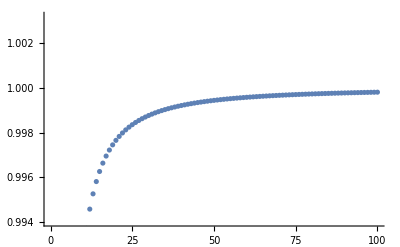

```mathematica
normratio25={};
For[i=1,i≤Length[normcoef25]-1,++i,
AppendTo[normratio25,normcoef25[[i+1]]/normcoef25[[i]]]
];

Show[ListPlot[normratio25]]
```